```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/fluctuations_T/highorder_2p1/PQM2p1flavor/data

```mathematica
T=Flatten[Table[i,{i,11,260,1}]];
chi0=Flatten[Import["./chi0.dat"]];
chi1=Flatten[Import["./chi1.dat"]];
chi2=Flatten[Import["./chi2.dat"]];
chi3=Flatten[Import["./chi3.dat"]];
chi4=Flatten[Import["./chi4.dat"]];
chi5=Flatten[Import["./chi5.dat"]];
chi6=Flatten[Import["./chi6.dat"]];
chi7=Flatten[Import["./chi7.dat"]];
chi8=Flatten[Import["./chi8.dat"]];
```

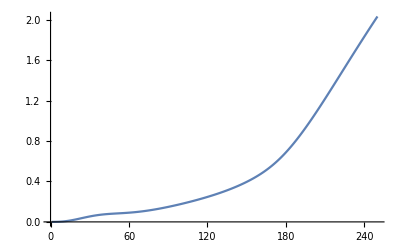

```mathematica
ListLinePlot[chi0/T^4,PlotRange->All]
```